```mathematica
dual=Map[Simplify,Select[Table[allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0],{k,Keys[allGraphs]}],Length[ListofVars[#]]==2&]]
```

{n1x2x3x4x5>n12x3x4x5,n1x2345>n12345,n15x234>n12345,n1x234x5>n1234x5,n14x235≥n12345,n145x23>n12345,n14x23x5>n1234x5,n1x235x4>n1235x4,n15x23x4>n1235x4,n1x23x4x5>n123x4x5,n1x23x45>n123x45,n13x2x4x5>n123x4x5,n13x245≥n12345,n135x24≥n12345,n13x24x5≥n1234x5,n134x2x5>n1234x5,n134x25≥n12345,n1345x2>n12345,n13x25x4≥n1235x4,n135x2x4>n1235x4,n13x2x45>n123x45,n1x245x3>n1245x3,n15x24x3>n1245x3,n1x24x3x5>n124x3x5,n1x24x35>n124x35,n14x2x3x5>n124x3x5,n14x25x3≥n1245x3,n145x2x3>n1245x3,n14x2x35>n124x35,n1x25x3x4>n125x3x4,n1x25x34>n125x34,n15x2x3x4>n125x3x4,n15x2x34>n125x34,n1x2x34x5>n12x34x5,n1x2x345>n12x345,n1x2x35x4>n12x35x4,n1x2x3x45>n12x3x45,n12x3x4x5>n123x4x5,n12x345>n12345,n125x34>n12345,n12x34x5>n1234x5,n124x3x5>n1234x5,n124x35≥n12345,n1245x3>n12345,n12x35x4>n1235x4,n125x3x4>n1235x4,n12x3x45>n123x45,n123x4x5>n1234x5,n123x45>n12345,n1235x4>n12345,n1234x5>n12345,n123x4x5>n1235x4,n123x4x5>n123x45,n12x3x4x5>n124x3x5,n12x3x45>n1245x3,n125x3x4>n1245x3,n12x35x4>n124x35,n124x3x5>n1245x3,n124x3x5>n124x35,n12x3x4x5>n125x3x4,n12x34x5>n125x34,n125x3x4>n125x34,n12x3x4x5>n12x34x5,n12x3x45>n12x345,n12x35x4>n12x345,n12x34x5>n12x345,n12x3x4x5>n12x35x4,n12x3x4x5>n12x3x45,n1x2x3x4x5>n13x2x4x5,n1x2x345>n1345x2,n15x2x34>n1345x2,n1x25x34>n134x25,n1x2x34x5>n134x2x5,n14x2x3x5>n134x2x5,n14x2x35≥n1345x2,n145x2x3>n1345x2,n14x25x3>n134x25,n1x24x35>n135x24,n1x2x35x4>n135x2x4,n15x2x3x4>n135x2x4,n15x24x3>n135x24,n1x24x3x5>n13x24x5,n1x245x3>n13x245,n1x25x3x4>n13x25x4,n1x2x3x45>n13x2x45,n13x2x4x5>n134x2x5,n13x2x45>n1345x2,n135x2x4>n1345x2,n13x25x4>n134x25,n134x2x5>n1345x2,n134x2x5>n134x25,n13x2x4x5>n135x2x4,n13x24x5>n135x24,n135x2x4>n135x24,n13x2x4x5>n13x24x5,n13x2x45>n13x245,n13x25x4>n13x245,n13x24x5>n13x245,n13x2x4x5>n13x25x4,n13x2x4x5>n13x2x45,n1x2x3x4x5>n14x2x3x5,n1x23x45>n145x23,n1x2x3x45>n145x2x3,n15x2x3x4>n145x2x3,n15x23x4>n145x23,n1x23x4x5>n14x23x5,n1x235x4>n14x235,n1x25x3x4>n14x25x3,n1x2x35x4>n14x2x35,n14x2x3x5>n145x2x3,n14x23x5>n145x23,n145x2x3>n145x23,n14x2x3x5>n14x23x5,n14x2x35>n14x235,n14x25x3>n14x235,n14x23x5>n14x235,n14x2x3x5>n14x25x3,n14x2x3x5>n14x2x35,n1x2x3x4x5>n15x2x3x4,n1x23x4x5>n15x23x4,n1x234x5>n15x234,n1x24x3x5>n15x24x3,n1x2x34x5>n15x2x34,n15x2x3x4>n15x23x4,n15x2x34>n15x234,n15x24x3>n15x234,n15x23x4>n15x234,n15x2x3x4>n15x24x3,n15x2x3x4>n15x2x34,n1x2x3x4x5>n1x23x4x5,n1x2x345>n1x2345,n1x25x34>n1x2345,n1x2x34x5>n1x234x5,n1x24x3x5>n1x234x5,n1x24x35≥n1x2345,n1x245x3>n1x2345,n1x2x35x4>n1x235x4,n1x25x3x4>n1x235x4,n1x2x3x45>n1x23x45,n1x23x4x5>n1x234x5,n1x23x45>n1x2345,n1x235x4>n1x2345,n1x234x5>n1x2345,n1x23x4x5>n1x235x4,n1x23x4x5>n1x23x45,n1x2x3x4x5>n1x24x3x5,n1x2x3x45>n1x245x3,n1x25x3x4>n1x245x3,n1x2x35x4>n1x24x35,n1x24x3x5>n1x245x3,n1x24x3x5>n1x24x35,n1x2x3x4x5>n1x25x3x4,n1x2x34x5>n1x25x34,n1x25x3x4>n1x25x34,n1x2x3x4x5>n1x2x34x5,n1x2x3x45>n1x2x345,n1x2x35x4>n1x2x345,n1x2x34x5>n1x2x345,n1x2x3x4x5>n1x2x35x4,n1x2x3x4x5>n1x2x3x45}

```mathematica
Select[dual,ToString[#[[0]]]≠"Greater"&]
```

{n14x235≥n12345,n13x245≥n12345,n135x24≥n12345,n13x24x5≥n1234x5,n134x25≥n12345,n13x25x4≥n1235x4,n14x25x3≥n1245x3,n124x35≥n12345,n14x2x35≥n1345x2,n1x24x35≥n1x2345}

```mathematica
realDemoValues=Table[allGraphs[k,"colofourrealnull"]->allGraphs[k,"colofour"]/.demoValues,{k,realyNullAtomKeys}]
```

{n1x2x3x4x5→3728,n1x2x3x45→1208,n1x2x35x4→728,n1x2x34x5→1240,n1x2x345→364,n1x25x3x4→876,n1x25x34→328,n1x24x3x5→876,n1x24x35→200,n1x245x3→262,n1x23x4x5→1380,n1x23x45→450,n1x235x4→262,n1x234x5→438,n1x2345→131,n15x2x3x4→1344,n15x2x34→452,n15x24x3→340,n15x23x4→496,n15x234→170,n14x2x3x5→1112,n14x2x35→232,n14x25x3→256,n14x23x5→446,n14x235→98,n145x2x3→524,n145x23→211,n13x2x4x5→1088,n13x2x45→340,n13x25x4→274,n13x24x5→286,n13x245→96,n135x2x4→272,n135x24→96,n134x2x5→344,n134x25→106,n1345x2→136,n12x3x4x5→1368,n12x3x45→406,n12x35x4→292,n12x34x5→478,n12x345→146,n125x3x4→420,n125x34→163,n124x3x5→344,n124x35→93,n1245x3→136,n123x4x5→544,n123x45→170,n1235x4→136,n1234x5→172,n12345→68}

```mathematica
realDemoValuesNotEmbedded=Table[allGraphs[k,"colofourrealnull"]->ChromaticPolynomial[ allGraphs[k,"graph"],4],{k,realyNullAtomKeys}]
```

{n1x2x3x4x5→1024,n1x2x3x45→256,n1x2x35x4→256,n1x2x34x5→256,n1x2x345→64,n1x25x3x4→256,n1x25x34→64,n1x24x3x5→256,n1x24x35→64,n1x245x3→64,n1x23x4x5→256,n1x23x45→64,n1x235x4→64,n1x234x5→64,n1x2345→16,n15x2x3x4→256,n15x2x34→64,n15x24x3→64,n15x23x4→64,n15x234→16,n14x2x3x5→256,n14x2x35→64,n14x25x3→64,n14x23x5→64,n14x235→16,n145x2x3→64,n145x23→16,n13x2x4x5→256,n13x2x45→64,n13x25x4→64,n13x24x5→64,n13x245→16,n135x2x4→64,n135x24→16,n134x2x5→64,n134x25→16,n1345x2→16,n12x3x4x5→256,n12x3x45→64,n12x35x4→64,n12x34x5→64,n12x345→16,n125x3x4→64,n125x34→16,n124x3x5→64,n124x35→16,n1245x3→16,n123x4x5→64,n123x45→16,n1235x4→16,n1234x5→16,n12345→4}

```mathematica
values3=Map[#[[2]]/#[[1]]/.realDemoValuesNotEmbedded&,dual]
```

{1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4,1/4}

```mathematica
values2=Map[#[[2]]/#[[1]]/.realDemoValues&,dual]
```

{171/466,68/131,2/5,86/219,34/49,68/211,86/223,68/131,17/62,136/345,17/45,1/2,17/24,17/24,86/143,1/2,34/53,1/2,68/137,1/2,1/2,68/131,2/5,86/219,93/200,43/139,17/32,34/131,93/232,35/73,163/328,5/16,163/452,239/620,73/182,73/182,203/604,68/171,34/73,68/163,86/239,1/2,68/93,1/2,34/73,34/105,85/203,43/136,2/5,1/2,17/43,1/4,5/16,43/171,68/203,34/105,93/292,17/43,93/344,35/114,163/478,163/420,239/684,73/203,1/2,73/239,73/342,203/684,68/233,34/91,34/113,53/164,43/155,43/139,17/29,34/131,53/128,12/25,34/91,17/84,24/85,143/438,48/131,137/438,85/302,43/136,2/5,1/2,53/137,17/43,53/172,1/4,48/143,6/17,143/544,24/85,48/137,48/143,137/544,5/16,139/466,211/450,131/302,131/336,211/496,223/690,49/131,64/219,29/91,131/278,211/446,211/524,223/556,49/116,49/128,49/223,32/139,29/139,84/233,124/345,85/219,85/219,113/310,31/84,85/226,1/2,85/248,85/336,113/336,345/932,131/364,131/328,219/620,1/2,131/200,1/2,131/364,131/438,225/604,73/230,131/450,1/2,131/438,131/690,15/46,219/932,131/604,131/438,25/91,131/438,50/219,219/932,41/155,82/219,155/466,91/302,1/2,91/310,91/466,151/466}

```mathematica
values=Map[(#[[2]]/#[[1]]/.repPlantri8)&,dual]
```

{60/157,16/27,16/27,8/17,4/5,4/7,4/7,34/59,34/73,41/96,28/65,1/2,4/5,16/21,8/11,1/2,16/25,1/2,34/55,1/2,1/2,34/59,17/29,17/35,21/37,17/41,34/55,17/41,21/44,99/205,14/31,33/80,3/7,49/130,27/68,29/70,73/192,41/120,16/27,8/21,16/49,8/17,16/21,8/17,17/29,34/99,28/73,16/41,4/7,8/17,1/2,17/41,14/41,17/60,34/73,34/99,21/58,1/2,21/68,33/80,3/7,14/33,49/120,27/73,27/58,27/98,29/120,73/240,41/157,8/17,16/49,25/93,16/65,16/41,8/11,16/41,5/11,21/37,17/35,17/60,21/58,11/35,20/59,11/41,7/24,16/41,4/7,8/17,5/11,1/2,25/64,17/41,21/44,21/68,11/41,5/14,4/11,5/11,55/164,14/41,41/157,28/65,41/96,41/120,28/73,7/24,20/59,11/41,11/35,1/2,1/2,14/41,14/41,5/11,4/11,5/14,55/164,11/41,60/157,73/192,27/68,29/70,49/130,73/240,27/98,27/58,27/73,29/120,49/120,48/157,27/68,9/31,17/65,17/35,27/37,27/59,59/140,59/205,65/192,17/48,27/65,27/59,27/68,59/192,65/192,35/157,59/192,59/205,37/140,59/140,37/140,205/628,93/260,93/205,65/157,17/48,17/35,17/65,35/157,48/157}

```mathematica
Select[Map[(#[[2]]/#[[1]]/.repPlantri8)->#&,dual],#[[1]]==4/5&]
```

{4/5→n14x235≥n12345,4/5→n13x245≥n12345}

```mathematica
N[{Min[values],Min[values2]}]
```

{0.22293,0.189855}

```mathematica
({n13x245,n14x235,n12345}/.repPlantri8) /24
```

{20,20,16}

```mathematica
({n13x245,n14x235,n12345}/.repcolofourrealnullgraph2)
```

{-Graphics-n13x24513340,-Graphics-n14x2354920,-Graphics-n1234559048}

```mathematica
allGraphs[13340]
```

<|signature→13340,matrix→{{2,0,2,0,0},{0,2,0,2,2},{2,0,2,0,0},{0,2,0,2,2},{0,2,0,2,2}},graph→-Graphics-,vertexsets→{{1,3},{2,4,5}},vertices→{1,2},edges→{},relations→{x13340==x36194+x59048,x13340==x36194+x59048,x13340==x36194+x59048,x13340==x36194+x59048,x13340==x36194+x59048,x13340==x36194+x59048,x13340==x13284-x13312,x13340==x13284-x13312,x13340==x13176-x13258,x13340==x13176-x13258,x13340==x13124-x13232,x13340==x13124-x13232,x13340==x218-x6779},links→{},parents→{13284,13284,13176,13176,13124,13124,218},children→{{36194,59048},{36194,59048},{36194,59048},{36194,59048},{36194,59048},{36194,59048}},comp→Greater,compwhy→The relation holds x13340== x36194(GreaterEqual) + 59048 (Greater),colofour→v12345+v13x245,colortable→{{v12345,v13x245},{v12345+v13x245,0},{v12345,v13x245},{v12345,v13x245},{v12345,v13x245},{v12345+v13x245,0},{v12345+v13x245,0},{v12345,v13x245},{v12345,v13x245},{v12345+v13x245,0}},colofournull→1/2 (-p13x245+p13x24x5+p13x25x4+p13x2x45-2 p13x2x4x5+p1x245x3-p1x24x3x5-p1x25x3x4-p1x2x3x45+2 p1x2x3x4x5),colofourrealnull→n13x245|>

```mathematica
Mean[values]//N
```

0.416434

```mathematica
Mean[values]//N
```

0.416434

```mathematica
Min[values]//N
```

0.22293

```mathematica
Max[values]
```

4/5

```mathematica
1/E//N
```

0.367879

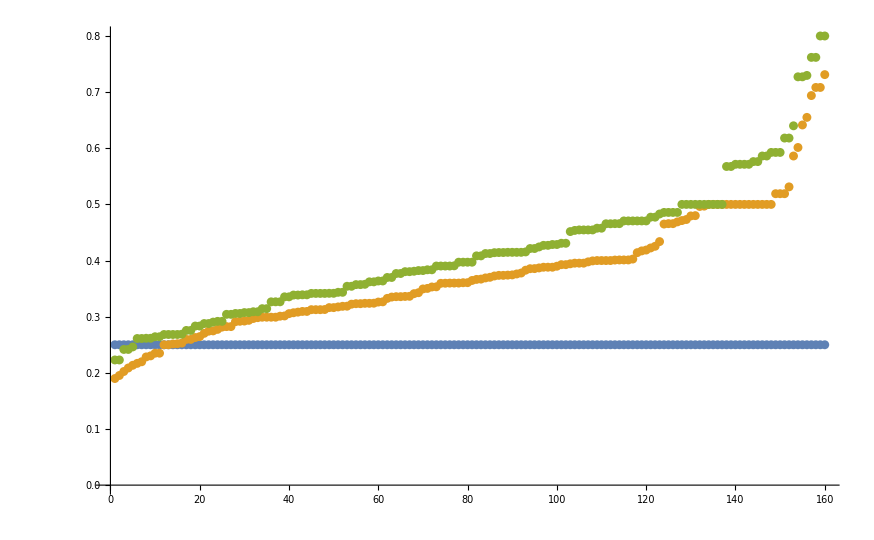

```mathematica
ListPlot[{Map[#[[2]]/#[[1]]/.realDemoValuesNotEmbedded&,dual]//Sort,Map[#[[2]]/#[[1]]/.realDemoValues&,dual]//Sort,Map[#[[2]]/#[[1]]/.repPlantri8&,dual]//Sort}, GridLines->{Automatic, {4/5,1/6}},GridLinesStyle->Directive[Red,Thick]]
```

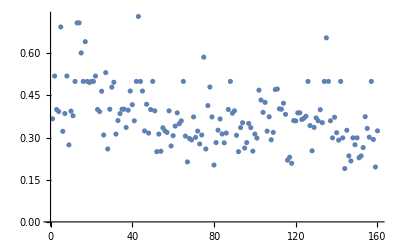

```mathematica
ListPlot[Map[#[[2]]/#[[1]]/.realDemoValues&,dual], GridLines->{{-1,0,1}, {1/10,4/5}}]
```

```mathematica
GoldenRatio[]
```

GoldenRatio[]

```mathematica
Table[allGraphs[k,"colofourrealnull"]/.realDemoValuesNotEmbedded,{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{24,24,24,24,24}

```mathematica
Table[allGraphs[k,"colofourrealnull"]/.realDemoValuesNotEmbedded,{k,{quad1Key,quad2Key,quad3Key,quad4Key}}]
```

{24,24,24,24}

```mathematica
ChromaticPolynomial[WheelGraph[6],4]
```

120

```mathematica
ListofVars[allGraphs[alfa1Key,"colofourrealnull"]]/.realDemoValuesNotEmbedded
```

{64,4,16,16,16}